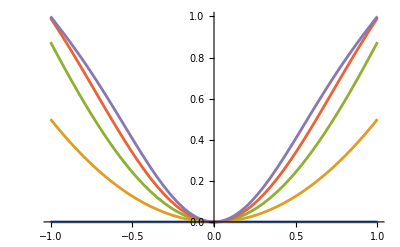

```mathematica
P[0]=0;
P[n_]:=P[n-1]+(x^2-P[n-1]^2)/2;

Plot[{P[0],P[1],P[2],P[3],P[4]},{x,-1,1}]
```